## Photon Sieve

The wavelength and focal length are taken to be (in meters)

```mathematica
λ=300 Quantity[, "Nanometers"]
```

300 nm

```mathematica
(*λ=303.8*10^-10;*)
f=2 Quantity[, "Meters"];
```

and the number of zones is taken to be

```mathematica
numZ=99;
```

Lets pick the packing factor (greater than 1) to be

```mathematica
α=1.5;
```

To get constructive interference at the focus, we need

```mathematica
zRad[n_]:=√(n λ f+(n^2 λ^2)/4)
```

The radius of each zone is then

```mathematica
zR1 = Array[zRad,numZ] // N;
zR2= Array[zRad,numZ,2] // N;
```

We can then calculate the width of each zone

```mathematica
zW=zR2-zR1;
Max[zW]
Min[zW]
```

320848. nm

38827.4 nm

The radius of each hole in the photon sieve is then

```mathematica
hR=zW /2;
```

and the distance of the center of each hole from the center of the photon sieve is

```mathematica
hC= zR1 + hR;
Min[hC]
Max[hC]
```

935021. nm

7.72657×10^6 nm

The circumference of a circle of radius hC is

```mathematica
hCirc=2 π hC;
```

The number of holes in each zone is then determined by the packing factor α

```mathematica
numH= Floor[hCirc/(zW α)];
```

The total number of holes is then

```mathematica
Total[numH]
```

41832

We can then find the angular location of each hole to be

```mathematica
hAngFunc[n_]:= Array[Identity,n]
```

```mathematica
hAng=2π Map[hAngFunc,numH]/numH;
```

Build plot of the photon sieve

```mathematica
holes={};
```

```mathematica
For[i=1,i<=Length[hC],i +=2,
For[j=1,j<=Length[hAng[[i]]],j++,
AppendTo[holes,Circle[{hC[[i]] Cos[hAng[[i,j]]],hC[[i]] Sin[hAng[[i,j]]]},hR[[i]]]]
]
]
```

$Aborted

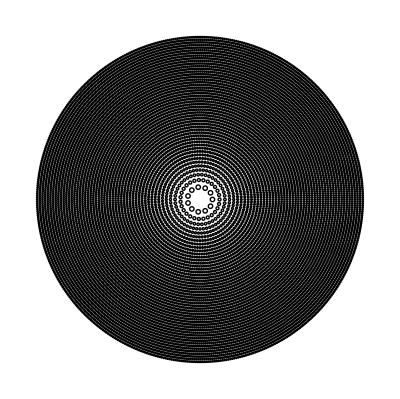

```mathematica
Graphics[holes]
```

The electric field diffracting through a circular hole in the Smythe-Kirchoff approximation is (Jackson 10.113) (assuming normal incidence)

```mathematica
Eh=TransformedField["Spherical"-> "Cartesian",(I E^(I k r))/r k a^2 E0 ({Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]} × {1,0,0})BesselJ[1,k a Sin[θ]]/(k a Sin[θ]),{r,θ,ϕ}-> {x,y,z}]
```

{(ⅈ a ⅇ^(ⅈ k √(x^2+y^2+z^2)) E0 x z^2 BesselJ[1,(a k √(x^2+y^2))/(√(x^2+y^2+z^2))])/((x^2+y^2) (x^2+y^2+z^2))+(ⅈ a ⅇ^(ⅈ k √(x^2+y^2+z^2)) E0 y^2 BesselJ[1,(a k √(x^2+y^2))/(√(x^2+y^2+z^2))])/((x^2+y^2) √(x^2+y^2+z^2)),(ⅈ a ⅇ^(ⅈ k √(x^2+y^2+z^2)) E0 y z^2 BesselJ[1,(a k √(x^2+y^2))/(√(x^2+y^2+z^2))])/((x^2+y^2) (x^2+y^2+z^2))-(ⅈ a ⅇ^(ⅈ k √(x^2+y^2+z^2)) E0 x y BesselJ[1,(a k √(x^2+y^2))/(√(x^2+y^2+z^2))])/((x^2+y^2) √(x^2+y^2+z^2)),-(ⅈ a ⅇ^(ⅈ k √(x^2+y^2+z^2)) E0 z BesselJ[1,(a k √(x^2+y^2))/(√(x^2+y^2+z^2))])/(x^2+y^2+z^2)}

The electric field of an offset hole is then

```mathematica
Eh=Eh/.{x-> x-x0,y-> y-y0,k-> 2 π / λ,E0-> 1.0};
```

```mathematica
Ehole=Compile[{{x0,_Real},{y0,_Real},{x,_Real},{y,_Real},{z,_Real},{a,_Real}},Evaluate[Eh]];
```

Create indices for parallel map

```mathematica
res=200;
xMax=Max[zR1];
xMin=-xMax;
yMax=Max[zR1];
yMin=-yMax;
zMax = f+1;
zMin = 0.0;
yDef = 0.00001;
xDef=0.0;
xRange = xMax-xMin;
yRange = yMax-yMin;
zRange = zMax-zMin;
xStep = xRange/res;
yStep = yRange/res;
zStep = zRange/res;
```

```mathematica
(*ptsXZ=ParallelTable[{x,z,Pps[x,yDef,z]},{x,xMin,xMax,xStep},{z,zMin,zMax,zStep}];*)
ptsXZ=ParallelTable[{x,z,Evaluate[Norm[Abs[Sum[Ehole[hC[[i]] Cos[hAng[[i,j]]],hC[[i]] Sin[hAng[[i,j]]],x,yDef,z,hR[[i]]],{i,1,Length[hC],2},{j,1,Length[hAng[[i]]]}]]]]},{x,xMin,xMax,xStep},{z,zMin,zMax,zStep}];//AbsoluteTiming
```

$Aborted

```mathematica
ListDensityPlot[Flatten[ptsXZ,1],PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

-Graphics-